```mathematica
A =   
{{8, 1, 11},
{4, 0, 4}, 
{-4, -3, -7}};

B = {{-1}, {-3}, {3}};
x0={1,1,1};

beta=-2.5;r=1.5;
K4 = {{-2.9881,0.9905,-2.9881}};

Acl4=A+B.K4;
xsol4[t_]=MatrixExp[Acl4 t].x0;
usol4[t_]=(K4.xsol4[t])[[1]];
eigs4=Eigenvalues[Acl4]
```

{-3.,-2.51037,-2.43733}

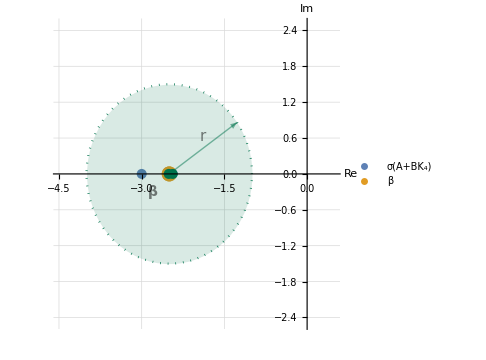

```mathematica
eigsPlot4 = Show[ListPlot[
{{Re[#],Im[#]}&/@eigs4,{{beta,0}}},
PlotStyle->{{PointSize[0.02],SilverColor},{PointSize[0.03],GoldenrodYellow}},
PlotRange->{{-4.5,0.5},{-2.5,2.5}},
Axes->True,
AxesLabel->{Style["Re"],Style["Im"]},
LabelStyle->{FontFamily->"Times New Roman",FontSize->14},
PlotLegends->Placed[LineLegend[{"σ(A+BK₄)","β"},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->14}],{0.65,0.95}],
GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],
AspectRatio->1, ImageSize->Medium
],

ParametricPlot[
{beta+r*Cos[t],r*Sin[t]},{t,0,2 Pi},
PlotStyle->{RGBColor[0.0,0.45,0.3],Dotted}
],

Graphics[
{RGBColor[0.0,0.45,0.3],Opacity[0.15],Disk[{beta,0},r],
RGBColor[0.0,0.45,0.3],Thick,Arrowheads[0.07],Opacity[0.5],
Arrow[{{beta,0},{beta+r*Cos[35 Degree],r*Sin[35 Degree]}}],
Black,Text[Style["r",FontSize->15,FontFamily->"Times New Roman"],
{beta+(r*Cos[35 Degree])/2,(r*Sin[35 Degree])/2+0.2}],
Black,Text[Style["β",FontSize->14,Bold, FontFamily->"Times New Roman"],{beta-0.3,-0.3}]}
],

Graphics[{RGBColor[0.0,0.45,0.3],PointSize[0.02],Point[{-2.510,0}]}], (*рисую руками, так как перекрыть желтую сложно.*)
Graphics[{RGBColor[0.0,0.45,0.3],PointSize[0.02],Point[{-2.437,0}]}]
]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task3/eig4.pdf"}],eigsPlot4];
```

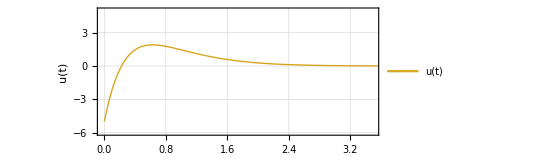

```mathematica
U4=Plot[usol4[t],{t,0,5},PlotStyle->{RGBColor[0.85,0.65,0.13],Thick},PlotLegends->Placed[LineLegend[{"u(t)"},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.87,0.9}],PlotRange->{{-0.02,3.5},{-6,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["u(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task3/U4.pdf"}],U4];
```

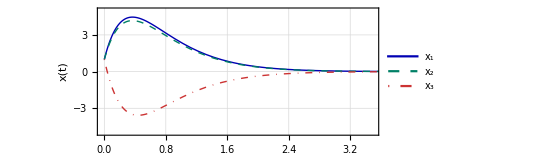

```mathematica
X4=Plot[{xsol4[t][[1]],xsol4[t][[2]],xsol4[t][[3]]},{t,0,5},PlotStyle->{{RGBColor[0,0,0.7],Thick},{RGBColor[0,0.5,0.4],Dashed,Thick},{RGBColor[0.8,0.2,0.2],DotDashed,Thick}},PlotLegends->Placed[LineLegend[{Subscript[x,1],Subscript[x,2],Subscript[x,3]},LegendLayout->"Row",LabelStyle->{FontFamily->"Times New Roman",FontSize->12}],{0.67,0.93}],PlotRange->{{-0.02,3.5},{-5,5}},Frame->True,Axes->False,FrameLabel->{Style["t",FontFamily->"Times New Roman",FontSize->12],Style["x(t)",FontFamily->"Times New Roman",FontSize->12]},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],AspectRatio->0.4]

Export[FileNameJoin[{NotebookDirectory[],"../../report/images/task3/X4.pdf"}],X4];
```